```mathematica
$VersionNumber
```

13.

Mathematica notebook comparing different Dirac Trace evaluation speeds. 
Rerunning benchmarks against other codes requires installation of 
TRACER
https://library.wolfram.com/infocenter/ID/2987/
FormTRACER
https://github.com/FormTracer/FormTracer
Feyncalc
https://feyncalc.github.io/ 
Note that this repo contains pre-computed timings (run on a Macbook M1 Pro), in the files “tracerResults,feyncalcResults,formtracerResults,tutteResults”, which can be used to reconstruct the timings figure in the paper.

### Generate Random Contractions

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Random Contractions*)
r[n_] := Insert[Insert[r[n - 1], n, RandomInteger[{1, 2 (n - 1) + 1}]], n, RandomInteger[{1, 2 n}]] /; n > 0;
r[n_] := {} /; n == 0;
```

Generate a bunch of contractions to test the different algorithms on

```mathematica
SeedRandom[0];
randomContractions=Table[r[n],{n,2,100,2},{i,1,128}];
Save["randomContractions",randomContractions];
```

### Compute Random Contractions with Mathematica’s Tutte-Polynomial

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["randomContractions"];
```

```mathematica
(*Circle Graph associated to a contraction*)
Clear[g];
g[l1_, l2_, l3_] := l3 /; Length[l2] == 0;
g[l1_, l2_, l3_] := g[DeleteCases[l1, l2[[1]]], Take[l2, {2, -1}], Join[l3, (l2[[1]] <-> #) & /@ Take[l1, {FirstPosition[l1, l2[[1]]][[1]] + 1, -1}]]] /; MemberQ[l1, l2[[1]]]; g[l1_, l2_, l3_] := g[Append[l1, l2[[1]]], Take[l2, {2, -1}], l3] /; ! MemberQ[l1, l2[[1]]];
(*Computes the d-dimensional Dirac Trace via a call to Mathematica's inbuilt TuttePolynomial*)
TutteTrace[x_]:=Module[{gx,c,e,L},
L = Length[x]/2;
gx=Graph[DeleteDuplicates[x],g[{},x,{}]];
c = Length[ConnectedComponents[gx]];
e = Length[EdgeList[gx]];
4 d^c(-1)^(c+e-L)2^(L-c)TuttePolynomial[gx,{1-d/2,-1}]
];
(*Computes the 4-dimensional Dirac Trace via computing dimension of bicycle space*)
TutteTrace4[x_]:=Module[{gx,c,L,im,ker},
gx=Graph[DeleteDuplicates[x],g[{},x,{}]];
c = Length[ConnectedComponents[gx]];
L = Length[x]/2;
If[Length[EdgeList[gx]]==0,Return[2^(2L+2)]];
im =Function[i,(If[#[[1]]==i || #[[2]]==i,1,0]&/@EdgeList[gx])]/@Range[L];
ker=NullSpace[Transpose[(Function[i,If[#[[1]]==i || #[[2]]==i,1,0]]/@Range[L])&/@EdgeList[gx]],Modulus->2];
(-1)^(c-L)2^(L+c+2)Power[-2,Length[NullSpace[Join[im,ker],Modulus->2]]]
];
```

```mathematica
tutteResults=Monitor[Table[AbsoluteTiming[TutteTrace[#[[i]]]//Expand],{i,128}],i]&/@Take[randomContractions,9];
```

```mathematica
Save["tutteResults",tutteResults];
```

### Compute Random Contractions with TRACER

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["randomContractions"];
```

```mathematica
<<Tracer`
```

Remove::rmnsm: There are no symbols matching "Tracer`Private`*".

T R A C E R

=============

A MATHEMATICA PACKAGE FOR GAMMA-ALGEBRA IN ARBITRARY DIMENSIONS

by M. Jamin and M.E. Lautenbacher

Physics Dept. T31, Technical University Munich

Version 1.1.1 from Mon Dec 30 15:36:00 MET 1991

(based on MATHEMATICA Version 1.2)

The package defines the following commands:

"AntiCommute", "ContractEpsGamma", "Eps", "G",
"GammaTrace", "G5", "H",
"ListCommands", "NoSpur",
"OnShell", "OutputFormat", "RemoveHatMomenta",

"RemoveNCM", "S", "Sigma", "SortLine", "Spur", "T",
"ToDiracBasis",
"ToHatTilde", "ToOtimes", "ToUG5", "U",
"VectorDimension", "Version".

                                    Help on usage as usual per ?Name.

DEFAULT SETTINGS ON STARTUP:

----------------------------

NonCommutativeMultiply will be removed.

Current OutputFormat is set to "texlike".

Package uses a non anticommuting G5 in "d" dimensions.

```mathematica
Spur[line1];
```

The gamma matrix line(s) "line1" will be traced.

```mathematica
tracerResults=Monitor[Table[AbsoluteTiming[G[line1,Sequence@@List/@#[[i]]]//Expand],{i,128}],i]&/@Take[randomContractions,7];
```

```mathematica
Save["tracerResults",tracerResults];
```

### Compute with FormTRACER

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["randomContractions"];
```

```mathematica
<<FormTracer`
```

FormTracer 2.3.7 loaded.

Copyright (C) 2013-2018, Anton K. Cyrol, Mario Mitter, Jan M. Pawlowski, and Nils Strodthoff.
FormTracer is released under the GNU General Public License version three or later.

If used in scientific publications, please acknowledge our work by citing:
A. K. Cyrol, M. Mitter, and N. Strodthoff, Comput. Phys. Commun. 219C (2017) 346-352, arXiv:1610.09331 [hep-ph]

Using FORM 4.2.1 (Nov  8 2022, v4.2.1-58-ge15da79) 64-bits.

```mathematica
DefineLorentzDimensions[d,4];
```

```mathematica
μs = {μ1, μ2, μ3, μ4, μ5, μ6, μ7, μ8, μ9, μ10, μ11, μ12, μ13, μ14, μ15, μ16, μ17, μ18, μ19, μ20,μ21,μ22,μ23,μ24,μ25,μ26,μ27,μ28,μ29,μ30,μ31,μ32,μ33,μ34,μ35,μ36,μ37,μ38,μ39,μ40,
μ41,μ42,μ43,μ44,μ45,μ46,μ47,μ48,μ49,μ50,μ51,μ52,μ53,μ54,μ55,μ56,μ57,μ58,μ59,μ60};
DefineLorentzTensors[deltaLorentz@@μs,vec[p,mu],sp[p,q],eps[],deltaDirac[i,j],gamma[mu,i,j],gamma5[i,j]];
```

```mathematica
formTracerResults=Monitor[Table[AbsoluteTiming[FormTrace[gamma[μs[[#[[i]]]]]]//Expand],{i,128}],i]&/@Take[randomContractions,9];
```

```mathematica
Save["formTracerResults",formTracerResults];
```

### Compute with FeynCalc

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["randomContractions"];
```

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
μs = {μ1, μ2, μ3, μ4, μ5, μ6, μ7, μ8, μ9, μ10, μ11, μ12, μ13, μ14, μ15, μ16, μ17, μ18, μ19, μ20,μ21,μ22,μ23,μ24,μ25,μ26,μ27,μ28,μ29,μ30,μ31,μ32,μ33,μ34,μ35,μ36,μ37,μ38,μ39,μ40};
```

```mathematica
feyncalcResults=Monitor[Table[AbsoluteTiming[DiracTrace[GAD[Sequence@@μs[[#[[i]]]]]]//DiracSimplify//Expand],{i,128}],i]&/@Take[randomContractions,8];
```

```mathematica
Save["feyncalcResults",feyncalcResults];
```

### Assert that everything works, make plots

```mathematica
Quit[];
```

```mathematica
<<MaTeX`
```

```mathematica
On[Assert];
SetDirectory[NotebookDirectory[]];
```

```mathematica
randomContractions=Get["randomContractions"];
tutteResults=Get["tutteResults"];
tracerResults=Get["tracerResults"];
formTracerResults=Get["formTracerResults"];
feyncalcResults=Get["feyncalcResults"];
```

```mathematica
tutteTraces=Function[x,#[[2]]&/@x]/@tutteResults;
tracerTraces=Function[x,#[[2]]&/@x]/@tracerResults;
formTracerTraces=Function[x,#[[2]]&/@x]/@formTracerResults;
feyncalcTraces=Function[x,#[[2]]&/@x]/@feyncalcResults;

tutteTimes=Function[x,#[[1]]&/@x]/@tutteResults;
tracerTimes=Function[x,#[[1]]&/@x]/@tracerResults;
formTracerTimes=Function[x,#[[1]]&/@x]/@formTracerResults;
feyncalcTimes=Function[x,#[[1]]&/@x]/@feyncalcResults;
```

```mathematica
Assert[Take[tutteTraces,Min[Length[tutteTraces],Length[tracerTraces]]]==Take[tracerTraces,Min[Length[tutteTraces],Length[tracerTraces]]]];
Assert[Take[tutteTraces,Min[Length[tutteTraces],Length[formTracerTraces]]]==Take[formTracerTraces,Min[Length[tutteTraces],Length[formTracerTraces]]]];
Assert[Take[tutteTraces,Min[Length[tutteTraces],Length[feyncalcTraces]]]==Take[feyncalcTraces,Min[Length[tutteTraces],Length[feyncalcTraces]]]/.{D->d}];
```

```mathematica
av[x_]:=Log[Mean[x]];
```

```mathematica
tuttePlot=ListPlot[Table[{2i,av[tutteTimes[[i]]]},{i,Length[tutteTraces]}],PlotStyle->ColorData[97,"ColorList"][[4]],PlotMarkers->{"★",Small}];
formTracerPlot=ListPlot[Table[{2i,av[formTracerTimes[[i]]]},{i,Length[formTracerTraces]}],PlotStyle->{ColorData[97,"ColorList"][[3]]},PlotMarkers->{"●",Tiny}];
tracerPlot=ListPlot[Table[{2i,av[tracerTimes[[i]]]},{i,Length[tracerTraces]}],PlotStyle->{ColorData[97,"ColorList"][[1]]},PlotMarkers->{"◆",Small}];
feyncalcPlot=ListPlot[Table[{2i,av[feyncalcTimes[[i]]]},{i,Length[feyncalcTraces]}],PlotStyle->ColorData[97,"ColorList"][[2]],PlotMarkers->{"■",Small}];
```

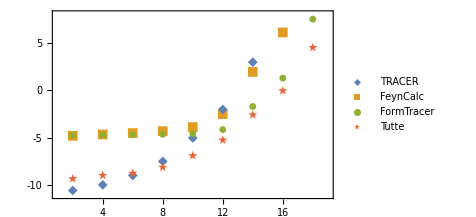

```mathematica
Show[feyncalcPlot,tracerPlot,tuttePlot,formTracerPlot,
PlotRange->{{1,19},{-11,8}},
Frame->True,
FrameLabel->{MaTeX["n",FontSize->12],MaTeX["\\ln(t)",FontSize->12]},
LabelStyle->{FontFamily->"CMU Serif",FontSize->12},
FrameTicks->{{{-10,-5,0,5},None} ,{{0,2,4,6,8,10,12,14,16,18},None}},
Epilog->Inset[PointLegend[Take[ColorData[97,"ColorList"],4],{"TRACER","FeynCalc","FormTracer                 ","Tutte"},LegendMarkers->{"◆","■","●","★"}],Scaled[{0.26,0.72}]],
RotateLabel->False,
Axes->False,
FrameStyle->Black
]
```